# Module 1

Excerpts are taken from:
Montgomery, Douglas, C. and George C. Runger. Applied Statistics and Probability for Engineers, Enhanced eText. Available from: WileyPLUS, (7th Edition). Wiley Global Education US, 2018.

## Lecture 1

## Setup

```mathematica
<<Notation`
```

```mathematica
Symbolize[OverBar[_]]
Symbolize[Subscript[_, _]]
```

```mathematica
PopulationVariance=ResourceFunction["PopulationVariance"]
```

```mathematica
SetOptions[DiscretePlot,PlotStyle->Thickness[.02],Frame->True];
SetOptions[Plot,PlotStyle->Thickness[.02],Frame->True];
```

## Win / Loss Example

Aside: highlight “//” and press F1 to see that this is “Postfix” syntax. Highlight “N” and press F1 to see that this gives this the numerical value of an expression. Fractions can be entered by typing the numerator, Ctrl+/, followed by the denominator. In the menu bar, click “Palletes” → “Basic Math Assistant” → “Typesetting” and hover your mouse over

```mathematica
Subscript[P, win]=20/100//N
```

0.2

```mathematica
Subscript[P, loss]=80/100//N
```

0.8

```mathematica
Subscript[P, win]+Subscript[P, loss]==1
```

True

## Rolling Dice

```mathematica
RandomChoice[{"Heads","Tails"}]
```

Tails

```mathematica
RandomInteger[{1,6}]
```

1

```mathematica
RollDi:=RandomInteger[{1,6}]
```

```mathematica
RollDi
```

1

Roll a Die “n” number of times

```mathematica
RollDice[n_]:=RandomInteger[{1,6},n]
```

```mathematica
rolls=RollDice[#]&/@{100,10000,1000000};
```

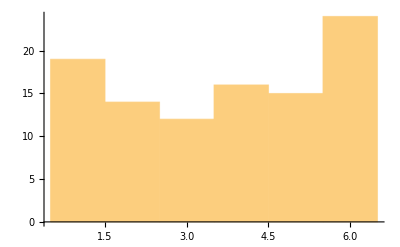
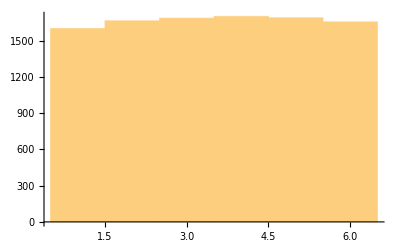
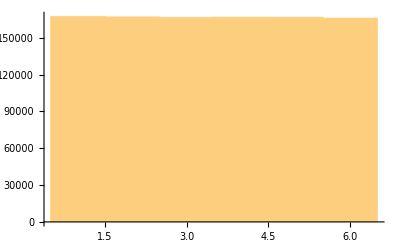

```mathematica
Histogram/@rolls
```

```mathematica
p=1/6;
diProbabilities=Association@Table[i->p,{i,1,6}]
```

<|1→1/6,2→1/6,3→1/6,4→1/6,5→1/6,6→1/6|>

```mathematica
Total@Values@diProbabilities==1
```

True

```mathematica
diNumbers=Range[6]
```

{1,2,3,4,5,6}

```mathematica
diRules=Thread[x==diNumbers]
```

{x==1,x==2,x==3,x==4,x==5,x==6}

Each number on a die has equal probability of being rolled.

```mathematica
diProbabilities=ConstantArray[1/6,6]
```

{1/6,1/6,1/6,1/6,1/6,1/6}

```mathematica
pw=Piecewise[{diProbabilities,diRules}ᵀ]
```

Piecewise[{{1/6, x==1||x==2||x==3||x==4||x==5||x==6}, {0, True}}]

What is the probability of rolling a 1?
(Aside: The following line of code can be read as follows, “pw with x replaced by 1”)

```mathematica
pw/.x->1
```

1/6

What is the probability of rolling a 1, 2, or 3?

```mathematica
p=pw/.x->#&/@{1,2,3}
```

{1/6,1/6,1/6}

```mathematica
Total[p]
```

1/2

## Lecture 2

## Digital Channel (Ex 3.3)

-Graphics-

```mathematica
digitalChannel=Piecewise[{{0.6561, x==0}, {0.2916, x==1}, {0.0486, x==2}, {0.0036, x==3}, {0.0001, x==4}}];
```

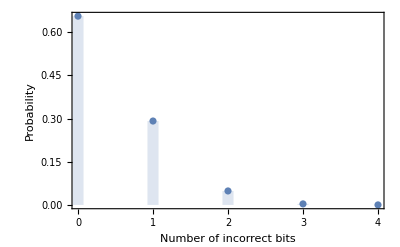

```mathematica
DiscretePlot[digitalChannel,{x,0,4},FrameLabel->{"Number of incorrect bits","Probability"}]
```

## Lecture 3

## Digital Channel (Ex 3.5)

-Graphics-

### Ways to access values from Piecewise

```mathematica
values=digitalChannel⟦1,;;,1⟧
```

{0.6561,0.2916,0.0486,0.0036,0.0001}

```mathematica
values=digitalChannel/.x->#&/@Range[0,4]
```

{0.6561,0.2916,0.0486,0.0036,0.0001}

### Cumulative Sum

```mathematica
Accumulate@values
```

{0.6561,0.9477,0.9963,0.9999,1.}

### P(X ≤ 3)

```mathematica
Total[values⟦;;4⟧]
```

0.9999

## Lecture 4

## Digital Channel (Ex 3.7)

-Graphics-

### Discrete Distribution

```mathematica
dist=ProbabilityDistribution[digitalChannel,{x,0,4,1}]
```

ProbabilityDistribution[Piecewise[{{0.6561, x==0}, {0.2916, x==1}, {0.0486, x==2}, {0.0036, x==3}, {0.0001, x==4}, {0, True}}],{x,0,4,1}]

### Expectation Value (several methods)

```mathematica
x[i_]:=i
```

```mathematica
f[i_]:=digitalChannel/.x->i
```

```mathematica
μ=0 f[0]+1 f[1]+2 f[2]+3 f[3]+4 f[4]
```

0.4

```mathematica
μ=Range[0,4].values
```

0.4

The mean of a distribution gives the expectation value.

```mathematica
μ=Mean[dist]
```

0.4

### Standard Deviation

The variance can be computed manually using a sum.

```mathematica
V=∑_(i=0)^4 f[x[i]](x[i]-μ)^2
```

0.36

Note that this is variance of a distribution, which considers weights appropriately.

```mathematica
Variance@dist
```

0.36

```mathematica
σ=√V
```

0.6

```mathematica
Around[μ,√V]
```

0.40.6

## NiCd Battery (3.3.6)

### -Graphics-

```mathematica
battery=Piecewise[{{0.17, x==0}, {0.35, x==2}, {0.33, x==3}, {0.15, x==4}}];
```

#### -Graphics-

```mathematica
dist=ProbabilityDistribution[battery,{x,0,4,1}];
```

```mathematica
cdf=CDF[dist]
```

Function[x,Piecewise[{{0., x<0}, {0.17, 0≤x<2}, {0.52, 2≤x<3}, {0.85, 3≤x<4}, {1., True}}],Listable]

```mathematica
cdf[#]&/@Range[0,4]
```

{0.17,0.17,0.52,0.85,1.}

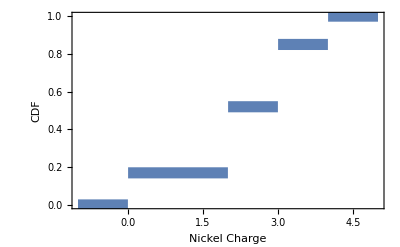

```mathematica
Plot[cdf[x],{x,-1,5},PlotRange->{0,1},FrameLabel->{"Nickel Charge","CDF"}]
```

```mathematica
cdf[4]
```

1.

#### -Graphics-

```mathematica
μ=Mean@dist
```

2.29

```mathematica
V=Variance@dist;
σ=√V
```

1.23527

```mathematica
charge=Around[μ,σ]
```

2.31.2

## Symbolic Mean and Variance

```mathematica
dummyValues=Piecewise[{{Subscript[p, 0], x=="a_0"}, {Subscript[p, 1], x=="a_1"}, {Subscript[p, 2], x=="a_2"}, {Subscript[p, 3], x=="a_3"}, {Subscript[p, 4], x=="a_4"}}];
```

```mathematica
x[i_]:=i
```

```mathematica
f[i_]:=dummyValues/.x->i
```

f[i] acts as a lookup function for the discrete probability.

```mathematica
{f["a_0"],f["a_1"],f["a_2"],f["a_3"],f["a_4"]}
```

{p_0,p_1,p_2,p_3,p_4}

```mathematica
f[5]
```

0

```mathematica
V=∑_(i=0)^4 f[x[i]](x[i]-μ)^2
```

0.

# Code Graveyard

## Exam Scores

```mathematica
(*scores=<|"50-60"->20,"61-80"->30,"81-100"->50|>*)
```

<|50-60→20,61-80→30,81-100→50|>

```mathematica
(*values=Values@scores;
total=Total@values;
values/total//N*)
```

{0.2,0.3,0.5}

```mathematica
(*Total[values/total]==1*)
```

True

### Piecewise Function

```mathematica
(*scores=Piecewise[{{20/(60-50), (x≥50)&&(x≤60)}, {30/(80-61), (x≥61)&&(x≤80)}, {50/(100-81), (x≥81)&&(x≤100)}}];*)
```

### Integration of First Group

```mathematica
(*(∫_50^60 scoresⅆx)/(∫_0^100 scoresⅆx)//N*)
```

0.2

### Integration of All Groups

```mathematica
(*MapThread[(∫_#1^#2 scoresⅆx)/(∫_0^100 scoresⅆx)&,{{50,61,81},{60,80,100}}]//N*)
```

{0.2,0.3,0.5}

## Probability Distribution

```mathematica
(*dist=ProbabilityDistribution[digitalChannel,{x,0,4,1}];
pdf=Simplify@PDF[dist,x];*)
```

```mathematica
(*DiscretePlot[pdf,{x,0,4},FrameLabel->{"Number of incorrect bits","Probability"}]*)
```

-Graphics-

```mathematica
(*dummyValues=Piecewise[{{Subscript[p, 0], x==Subscript[a, 0]}, {Subscript[p, 1], x==Subscript[a, 1]}, {Subscript[p, 2], x==Subscript[a, 2]}, {Subscript[p, 3], x==Subscript[a, 3]}, {Subscript[p, 4], x==Subscript[a, 4]}}];*)
```

```mathematica
(*$Assumptions=Subscript[a, 0]≠Subscript[a, 1]≠Subscript[a, 2]≠Subscript[a, 3]≠Subscript[a, 4]*)
```

a_0≠a_1≠a_2≠a_3≠a_4

```mathematica
(*x[i_]:=i*)
```

```mathematica
(*f[i_]:=dummyValues/.x->i*)
```

f[i] acts as a lookup function for the discrete probability.

```mathematica
(*{f[Subscript[a, 0]],f[Subscript[a, 1]],f[Subscript[a, 2]],f[Subscript[a, 3]],f[Subscript[a, 4]]}//FullSimplify*)
```

{p_0,p_1,p_2,p_3,p_4}

```mathematica
(*V=∑_(i=0)^4 f[x[i]](x[i]-μ)^2*)
```

5.2441 (Piecewise[{{p_0, 0==a_0}, {p_1, 0==a_1}, {p_2, 0==a_2}, {p_3, 0==a_3}, {p_4, 0==a_4}, {0, True}}])+1.6641 (Piecewise[{{p_0, 1==a_0}, {p_1, 1==a_1}, {p_2, 1==a_2}, {p_3, 1==a_3}, {p_4, 1==a_4}, {0, True}}])+0.0841 (Piecewise[{{p_0, 2==a_0}, {p_1, 2==a_1}, {p_2, 2==a_2}, {p_3, 2==a_3}, {p_4, 2==a_4}, {0, True}}])+0.5041 (Piecewise[{{p_0, 3==a_0}, {p_1, 3==a_1}, {p_2, 3==a_2}, {p_3, 3==a_3}, {p_4, 3==a_4}, {0, True}}])+2.9241 (Piecewise[{{p_0, 4==a_0}, {p_1, 4==a_1}, {p_2, 4==a_2}, {p_3, 4==a_3}, {p_4, 4==a_4}, {0, True}}])

```mathematica
(*Piecewise[{{0, x<0}, {0.17, 0≤x<2}, {0.35+0.17, 2≤x<3}, {0.33+0.35+0.17, 3≤x<4}, {0.15+0.33+0.35+0.17, True}}]*)
```

Piecewise[{{0, x<0}, {0.17, 0≤x<2}, {0.52, 2≤x<3}, {0.85, 3≤x<4}, {1., True}}]

# Print Notebook

Assumes that Mathematica notebook ends with .nb extension. Make sure the .pdf file is not open on the computer.

```mathematica
Export[StringDrop[NotebookFileName[],-2]<>"pdf",EvaluationNotebook[]]
```

C:\Users\sterg\Documents\GitHub\sparks-baird\mete-3070\mathematica\module-1.pdf